# The Energy Function of ^163 Lu

## Computing the Energy Function ℋ(I,θ,φ) for the nucleus

## ℋ=I/2(A_1+A_2)+A_3 I^2+I(I-1/2)sin^2 θ(A_1 cos^2 φ+A_2 sin^2 φ-A_3)+j/2(A_2+A_3)+A_1 j^2-2 A_1 Ij sinθ-V(2j-1)/(j+1)sin(γ+π/6);

### Constants (deformation parameters from actual fit)

```mathematica
A1=1/(2*73);
A2=1/(2*3);
A3=1/(2*67);
V=6.01;
j=13/2;
γ=21;
spinTSD1=14.5;
spinTSD2=45.5;
spinTSD3=30.5;
spinTSD4=39.5;
```

### Expression

```mathematica
Hen[I_,θ_,φ_]:=I/2(A1+A2)+A3*I^2+I(I-1/2)Sin[θ*π/180]^2(A1*Cos[φ*π/180]^2+A2*Sin[φ*π/180]^2-A3)+j/2(A2+A3)+A1*j^2-2A1*I*j*Sin[θ*π/180]-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
```

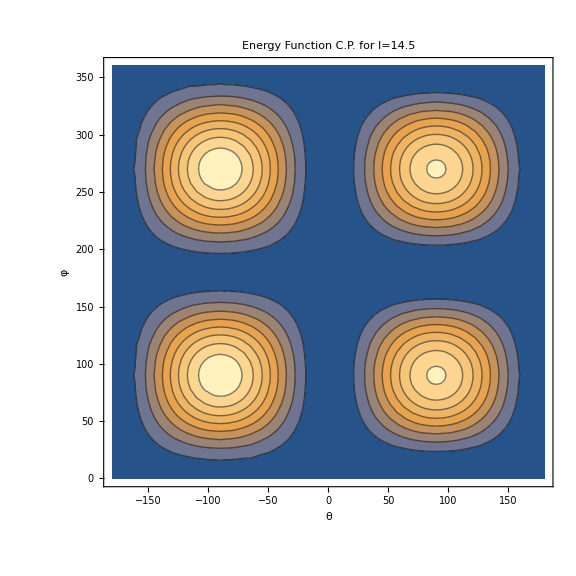

```mathematica
p1[spin_]:=ContourPlot[Hen[spin,θ,φ],{θ,-180,180},{φ,0,360},Frame->True,FrameStyle->Directive[Black,Thick],Contours->8,FrameLabel->{"θ","φ"},PlotLabel->StringTemplate["Energy Function \n C.P. for I=``"][spin],LabelStyle->{12,Black,Bold,FontFamily->"Times New Roman"},ImageSize->Large];
Show[p1[spinTSD1]]
(*Save the graph with the Contour Plot to an output file*)
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/ContourPlot.jpeg",pf];
```

## Graphics Grid with all the spins for the bands

```mathematica
pf=GraphicsGrid[{{Show[p1[spinTSD1]],Show[p1[spinTSD2]]},{Show[p1[spinTSD3]],Show[p1[spinTSD4]]}}];
```